# Test DAE for implicit Runge-Kutta integrators

## DAE and the corresponding ODE

The following DAE is solved:

0=∂_t x(t)+z(t)
0=x(t)-(z(t))^2

which corresponds to the following ODE

∂_t x(t)=-√(x(t))

```mathematica
ode={x'[t]==-√x[t],x[0]==x0};
```

### Solution of the ODE

{{x→Function[{t},1/4 (t^2-4 t √x0+4 x0)]},{x→Function[{t},1/4 (t^2+4 t √x0+4 x0)]}}

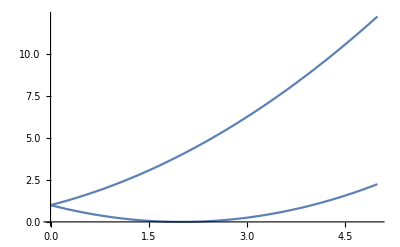

{1/4 (1-4 √x0+4 x0),1/4 (1+4 √x0+4 x0)}

```mathematica
sol=DSolve[ode,x,t]
Plot[x[t]/.sol/.x0->1,{t,0,5}]
x[1]/.sol
sol1=sol⟦1⟧;
```

{{x→InterpolatingFunction[{{0., 2.}}, <>]}}

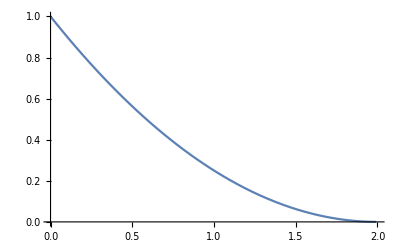

```mathematica
NDSolve[{x'[t]==-x[t]^(1/2),x[0]==1},x,{t,0,2}]
Plot[x[t]/.%,{t,0,2}]
```

```mathematica
x[t]/.sol1//FullSimplify
```

1/4 (t-2 √x0)^2

### Jacobian of the solution

```mathematica
D[x[t]/.sol1,x0]//FullSimplify
```

1-t/(2 √x0)

## Residual

```mathematica
r={x[t],3 √x[t]}/.sol1
```

{1/4 (t^2-4 t √x0+4 x0),3/2 √(t^2-4 t √x0+4 x0)}

### Jacobian of the residual

```mathematica
Jr=D[r,{{x0}}]//FullSimplify
```

{{1-t/(2 √x0)},{(3 (4-(2 t)/(√x0)))/(4 √((t-2 √x0)^2))}}

## Integral of Lagrange term

```mathematica
V=1/2∫_0^T r.rⅆt//FullSimplify
```

1/160 T (T^4-10 T^3 √x0+80 x0 (9+x0)+20 T^2 (3+2 x0)-40 T √x0 (9+2 x0))

### Gradient of integral of Lagrange term

```mathematica
g=D[V,x0]//FullSimplify
```

-(T (T-4 √x0) (36+T^2-4 T √x0+8 x0))/(32 √x0)

### Hessian of integral of Lagrange term

```mathematica
H=D[V,{{x0},2}]//FullSimplify
```

{{(T (T^3+T (36-24 x0)+64 x0^(3/2)))/(64 x0^(3/2))}}

### Gauss-Newton approximation of Hessian of integral of Lagrange term

```mathematica
Hgn=∫_0^T Transpose[Jr].Jrⅆt//FullSimplify
```

{{(T (27+T^2-6 T √x0+12 x0))/(12 x0)}}

### Numerical values for checking

```mathematica
{V,g,H,Hgn}/.{x0->1,T->1}//N
```

{2.81875,3.84375,{{1.20313}},{{2.83333}}}